```mathematica
Needs["INVARIANT`"]
```

## Input Seeds

```mathematica
Ecubic=-1399.68296559;
dir0="/home/paulchern/Documents/Workshop/Working/Boracites/ISOTROPY/PBEsolU/";
SeedSets=<|
"cubic"->"F-43c.iso192.allmodes.cif",
"p3"-> "00.00.00.001.000.000.iso.cif",
"p3e"->"00.00.00.001.111.111.iso.cif",
"p1p2p3"->"00.00.00.111.000.000.iso.cif",
"-p1-p2-p3"->"00.00.00.-1-1-1.000.000.iso.cif",
"c2"->"00.00.10.000.000.000.iso.cif",
"c1c2"->"00.00.11.000.000.000.iso.cif",
"c1c2e"->"00.00.11.000.111.111.iso.cif",
"c1c2p3"->"00.00.11.001.000.000.iso.cif",
"c1c2-3p"->"00.00.11.00-1.000.000.iso.cif",
"c1c2p3e"->"00.00.11.001.111.111.iso.cif",
"b2c2"->"00.01.10.000.000.000.iso.cif",
"b1c2"->"00.10.10.000.000.000.iso.cif",
"a2b2c2"->"0-1.01.10.000.000.000.iso.cif",
"a2b2c1c2p3"->"01.01.11.001.000.000.iso.cif",
"p1p2p3e"->"00.00.00.111.111.111.iso.cif"|>;
PhaseName="cubic";
fdist=dir0<>SeedSets[[PhaseName]];
Parent=ImportIsodistortCIF[dir0<>SeedSets[["cubic"]]];
SubGroup=ImportIsodistortCIF[fdist];
LatticeVectorsParent=N[Parent[[6]]/.Parent[[8]]];
LatticeVectorsSubGroup=N[SubGroup[[6]]/.SubGroup[[8]]];
Atoms=Parent[[7]];
Wyckoff0=Parent[[10]];
Wyckoff=SubGroup[[10]];
AtomsFrac=CifWyckoffImages[dir0<>SeedSets[["cubic"]],Wyckoff0];
IsoDim=Parent[[11]];
IsoSubDispModes=SubGroup[[12]];
IsoSubDispModeMatrix=SparseArray[Thread[Transpose[{Parent[[13]][[1]],Parent[[13]][[2]]}]->Parent[[13]][[3]]],{IsoDim,IsoDim}];
Subscript[ϵ, ij]=GetStrainTensor[Parent,SubGroup];
```

## Generate Training sets

#### microscopic modes

```mathematica
TrainingNum=11;
{modes,DirName}=GenTraningSets[IsoSubDispModes,TrainingNum,PhaseName,"p1p2"];
```

c1c2-p1p2 Generated.

```mathematica
Do[Print[ToString[ipos-(Quotient[TrainingNum,2]+1)]<>"%"];
DistortedWyckoffFrac=ImposeIsoMode[Wyckoff0,IsoSubDispModeMatrix,modes[[ipos]],1];
DistortedFrac=CifWyckoffImages[dir0<>SeedSets[["cubic"]],DistortedWyckoffFrac];
namedat=dir0<>"TrainingSets/"<>DirName<>"/"<>DirName<>"."<>ToString[ipos-(Quotient[TrainingNum,2]+1)]<>"%"<>".dat";
namevasp=dir0<>"TrainingSets/"<>DirName<>"/"<>DirName<>"."<>ToString[ipos-(Quotient[TrainingNum,2]+1)]<>"%"<>".vasp";
Export[namedat,Flatten/@Join[{{"From Mathematica"},{1}},LatticeVectorsSubGroup,{{"O", "Cl", "Cu", "B"},{104, 8, 24, 56}},{{"Direct"}},({#[[1]],#[[2]]}&/@DistortedFrac)],"Table","FieldSeparators"->"    "];
RenameFile[namedat,namevasp]
,{ipos,TrainingNum}]
```

-5%

-4%

-3%

-2%

-1%

0%

1%

2%

3%

4%

5%

#### Macroscopic modes (strains)

```mathematica
TrainingNum=11;
{StrainSets,DirName}=GenStrainSets[LatticeVectorsSubGroup,PhaseName, "gammac",TrainingNum];
```

gammac-cubic Generated.

```mathematica
Do[Print[DirName<>"."<>ToString[ipos-(Quotient[TrainingNum,2]+1)]<>"%"];
DistortedWyckoffFrac=ImposeIsoStrainVariedDspMode[Wyckoff0,IsoSubDispModeMatrix,IsoSubDispModes,StrainSets[[ipos]]];
DistortedFrac=CifWyckoffImages[dir0<>SeedSets[["cubic"]],DistortedWyckoffFrac];
namedat=dir0<>"TrainingSets/"<>DirName<>"/"<>DirName<>"."<>ToString[ipos-(Quotient[TrainingNum,2]+1)]<>"%"<>".dat";
namevasp=dir0<>"TrainingSets/"<>DirName<>"/"<>DirName<>"."<>ToString[ipos-(Quotient[TrainingNum,2]+1)]<>"%"<>".vasp";
Export[namedat,Flatten/@Join[{{"From Mathematica"},{1}},StrainSets[[ipos]],{{"O", "Cl", "Cu", "B"},{104, 8, 24, 56}},{{"Direct"}},({#[[1]],#[[2]]}&/@DistortedFrac)],"Table","FieldSeparators"->"    "];
RenameFile[namedat,namevasp]
,{ipos,TrainingNum}]
```

gammac-cubic.-5%

gammac-cubic.-4%

gammac-cubic.-3%

gammac-cubic.-2%

gammac-cubic.-1%

gammac-cubic.0%

gammac-cubic.1%

gammac-cubic.2%

gammac-cubic.3%

gammac-cubic.4%

gammac-cubic.5%

## Read in Training sets

{{gammac-cubic.0%,0.26647},{gammac-cubic.-1%,-9.02762},{gammac-cubic.1%,-6.54463},{gammac-cubic.-2%,-6.49633},{gammac-cubic.2%,-6.08861},{gammac-cubic.-3%,-4.24377},{gammac-cubic.3%,-2.1186},{gammac-cubic.-4%,-0.73059},{gammac-cubic.4%,2.05854},{gammac-cubic.-5%,7.25794},{gammac-cubic.5%,4.23418}}

{gammac-cubic.0%→0.26647,gammac-cubic.-1%→-9.02762,gammac-cubic.1%→-6.54463,gammac-cubic.-2%→-6.49633,gammac-cubic.2%→-6.08861,gammac-cubic.-3%→-4.24377,gammac-cubic.3%→-2.1186,gammac-cubic.-4%→-0.73059,gammac-cubic.4%→2.05854,gammac-cubic.-5%→7.25794,gammac-cubic.5%→4.23418}

{{0,0.26647},{-1,-9.02762},{1,-6.54463},{-2,-6.49633},{2,-6.08861},{-3,-4.24377},{3,-2.1186},{-4,-0.73059},{4,2.05854},{-5,7.25794},{5,4.23418}}

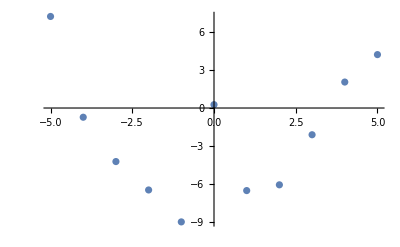

```mathematica
dircluster="/home/paulchern/QMT/Boracites/DFT/Cu3B7O13Cl/VASP/GGAU/Domains/TrainingSets";
DirTS=Table[DirName<>"."<>ToString[ipos-(Quotient[TrainingNum,2]+1)]<>"%",{ipos,TrainingNum}];
tsdata=Import[dircluster<>"/"<>DirName<>"/ts.dat","Table"];
tsdata={#[[1]],1000(#[[2]]-Ecubic)}&/@tsdata
tsdict=#[[1]]->#[[2]]&/@tsdata
pdata={ToExpression[StringSplit[#[[1]],{".","%"}][[2]]],#[[2]]}&/@tsdata
ListPlot[pdata]
```

```mathematica
Polynomial[vars_List,n_Integer,coeff_]:=Module[{varlist,poly},
poly=#.(Subscript[a, #]&/@Range[0,Length@#-1])&@DeleteDuplicates[Times@@@Tuples[Prepend[vars,1],n]];
varlist=Variables@poly;
Return[{poly,varlist}]]
```

```mathematica
Minimize[Total[(Polynomial[{#1},4,a][[1]]-#2)^2&@@@pdata],Subscript[a, #]&/@Range[0,4]]
```

{51.5131,{a_0→-5.43391,a_1→0.853483,a_2→0.110845,a_3→-0.0440732,a_4→0.0139173}}

```mathematica
Minimize[Total[(Polynomial[{#1},4,a][[1]]-#2)^2&@@@pdata[[2;;]]],Subscript[a, #]&/@Range[0,4]]
```

{6.07013,{a_0→-7.70544,a_1→0.709242,a_2→0.461727,a_3→-0.0371966,a_4→0.00316853}}

```mathematica
FittingSet=Table[ts=ImportIsodistortCIF[dircluster<>"/"<>DirName<>"/"<>tsname<>"/CONTCAR.cif"];
pos=ts[[10]];
LV=N[ts[[6]]/.ts[[8]]];
DspMode=ISODISTORT[LV,Wyckoff0,pos,IsoSubDispModeMatrix,IsoSubDispModesᵀ[[2]]];
Join[{tsname,tsname/.tsdict},GetX5mode[DspMode],GetPmode[DspMode],GetStrain[Parent,ts]]
,{tsname,DirTS}]
```

{{gammac-cubic.-5%,7.25794,0,0,0,0,0,0,0,0,0,4.99637×10^-6,1.00838×10^-6,-3.00362×10^-6,-0.000997496,-0.0010015,-0.000999496},{gammac-cubic.-4%,-0.73059,0,0,0,0,0,0,0,0,0,3.19799×10^-6,6.44136×10^-7,-1.92201×10^-6,-0.000798398,-0.000800958,-0.000799678},{gammac-cubic.-3%,-4.24377,0,0,0,0,0,0,0,0,0,1.79947×10^-6,3.62065×10^-7,-1.08053×10^-6,-0.000599099,-0.000600539,-0.000599819},{gammac-cubic.-2%,-6.49633,0,0,0,0,0,0,0,0,0,7.99333×10^-7,1.60102×10^-7,-4.80666×10^-7,-0.0003996,-0.00040024,-0.00039992},{gammac-cubic.-1%,-9.02762,0,0,0,0,0,0,0,0,0,2.00285×10^-7,4.03814×10^-8,-1.19715×10^-7,-0.0001999,-0.00020006,-0.00019998},{gammac-cubic.0%,0.26647,0,0,0,0,0,0,0,0,0,0.,0.,0.,0.,0.,0.},{gammac-cubic.1%,-6.54463,0,0,0,0,0,0,0,0,0,2.00349×10^-7,4.02534×10^-8,-1.19651×10^-7,0.0002001,0.00019994,0.00020002},{gammac-cubic.2%,-6.08861,0,0,0,0,0,0,0,0,0,7.99845×10^-7,1.59078×10^-7,-4.80154×10^-7,0.0004004,0.00039976,0.00040008},{gammac-cubic.3%,-2.1186,0,0,0,0,0,0,0,0,0,1.8012×10^-6,3.58609×10^-7,-1.0788×10^-6,0.000600899,0.000599459,0.000600179},{gammac-cubic.4%,2.05854,0,0,0,0,0,0,0,0,0,3.20208×10^-6,6.35944×10^-7,-1.91791×10^-6,0.000801598,0.000799038,0.000800318},{gammac-cubic.5%,4.23418,0,0,0,0,0,0,0,0,0,5.00437×10^-6,9.92379×10^-7,-2.99562×10^-6,0.0010025,0.000998496,0.0010005}}

```mathematica
Export["/home/paulchern/Documents/Workshop/Working/Boracites/ISOTROPY/PBEsolU/TrainingSets/"<>DirName<>"/"<>DirName<>".dat",FittingSet,"Table","FieldSeparators"->"\t","LineSeparators"->"\n"];
```

## Debug

```mathematica
Do[ts=ImportIsodistortCIF[dir0<>SeedSets[[k]]];
pos=ts[[10]];
LV=N[ts[[6]]/.ts[[8]]];
DspMode=ts[[12]];
Print[{k,Join[GetX5mode[DspMode],GetPmode[DspMode],GetStrain[Parent,ts]]}],
{k,Keys@SeedSets}]
```

{all,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{p3,{0.,0.,0.,0.,0.,0.,0.,0.,-0.889149,0.,0.,0.,0.,0.,0.}}

{p3e,{0.,0.,0.,0.,0.,0.,0.,0.,-0.901556,0.000551312,0.000538712,0.000715009,-0.00177579,0.,0.}}

{p1p2p3,{0.,0.,0.,0.,0.,0.,-0.717634,-0.717634,-0.717634,0.,0.,0.,0.,0.,0.}}

{-p1-p2-p3,{0.,0.,0.,0.,0.,0.,0.608259,0.608259,0.608259,0.,0.,0.,0.,0.,0.}}

{c2,{0.,0.,0.,0.,0.,0.827251,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{c1c2,{0.,0.,0.,0.,0.699051,0.699051,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{c1c2e,{0.,0.,0.,0.,0.713794,0.713794,0.,0.,0.,0.000456292,0.000450443,0.0013475,0.0012097,0.,0.}}

{c1c2p3,{0.,0.,0.,0.,1.21217,1.21217,0.,0.,-1.45179,0.,0.,0.,0.,0.,0.}}

{c1c2-3p,{0.,0.,0.,0.,0.6847,0.6847,0.,0.,0.646338,0.,0.,0.,0.,0.,0.}}

{c1c2p3e,{0.,0.,0.,0.,1.26771,1.26771,0.,0.,-1.52893,0.00428965,0.00426344,0.0037937,0.00257061,0.,0.}}

{b2c2,{0.,0.,0.,0.708924,0.660653,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{b1c2,{0.,0.,0.496566,0.,-0.496566,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{a2b2c2,{0.,-1.00355,0.,1.00366,1.00357,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{a2b2c1c2p3,{0.,0.474462,0.,-0.807585,0.858148,-0.617447,0.,0.,0.340624,0.,0.,0.,0.,0.,0.}}

{p1p2p3e,{0.,0.,0.,0.,0.,0.,-0.735097,-0.735097,-0.735097,0.00116129,0.00116118,0.00116106,-0.000169831,-0.000169946,-0.000169888}}